# ActoNet : Data import, analysis and formatting

## Data Import

The database contains all (178) patients profiles sorted by the number of perturbations in the profiles of the dataset together with the clinical data. 
The profiles correspond to sets in which mutated genes (TP53,PI3K,RAS, FGFR3) are present or absent and CNV genes (E2F3,EGFR,CyclinD1,MDM2, p16INK4A,RB1,RBL2) may be amplified (gene->True) or deleted (gene->False).

```mathematica
database=TernaryDataFormatting[FILENAME$]
```

Dataset[<>]

## Data Analysis

#### Frequence of each perturbation on the complete database

```mathematica
PerturbationFrequence[Normal@database[All,"profile"]]
```

FGFR3 | PI3K | RAS | TP53 | CyclinD1→False | CyclinD1→True | E2F3→False | E2F3→True | EGFR→False | EGFR→True | MDM2→False | MDM2→True | p16INK4a→False | p16INK4a→True | RB1→False | RB1→True | RBL2→False | RBL2→True
33.7 | 8.99 | 6.74 | 32. | 5.62 | 36.5 | 5.06 | 24.2 | 6.18 | 21.9 | 4.49 | 20.2 | 45.5 | 2.81 | 20.2 | 5.62 | 17.4 | 6.18

#### Distribution of the number of perturbations

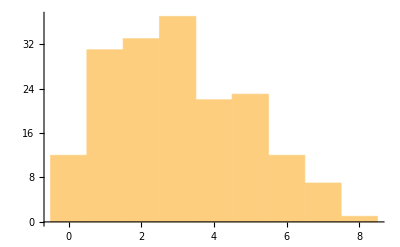

```mathematica
PerturbationNumberDistribution[Normal@database[All,"profile"]]
```

#### Profiles appearing more than once

```mathematica
Map[Tally,Select[Gather[Normal@database[All,"profile"]],Length[#]>1&]]
```

{{{{},12}},{{{RBL2→False},2}},{{{FGFR3},14}},{{{TP53},2}},{{{p16INK4a→False},2}},{{{CyclinD1→True},2}},{{{MDM2→True},3}},{{{E2F3→True},2}},{{{RAS},2}},{{{FGFR3,CyclinD1→False},2}},{{{FGFR3,p16INK4a→False},5}},{{{FGFR3,PI3K},4}},{{{FGFR3,CyclinD1→True},2}},{{{FGFR3,TP53},2}},{{{FGFR3,RB1→False},3}},{{{E2F3→False,p16INK4a→False},2}},{{{FGFR3,MDM2→True,p16INK4a→False},2}},{{{CyclinD1→True,MDM2→True,p16INK4a→False},4}},{{{TP53,E2F3→True,EGFR→True},2}},{{{TP53,CyclinD1→True,RB1→False},4}},{{{FGFR3,CyclinD1→True,p16INK4a→False},2}},{{{FGFR3,CyclinD1→True,p16INK4a→False,RBL2→False},2}},{{{TP53,CyclinD1→True,E2F3→True,EGFR→True,MDM2→True},2}}}

## Profiles curation

### Deletion of duplicates and empty profiles

By eliminating the profiles containing no perturbations we end up with a database containing 166 profiles (12 empty profiles)

```mathematica
WithoutEmptyProfiles=database[Select[#profile≠{}&]]
```

Dataset[<>]

There is 121 different molecular profiles.

```mathematica
Length[WithoutDuplicates=Sort/@DeleteDuplicates[Normal@WithoutEmptyProfiles[All,"profile"]]]
```

121

### ProfileSet

Since the inferred solutions contain 3 perturbations, we keep only the profiles containing at least three perturbations for comparison

```mathematica
ProfileSet=Select[WithoutDuplicates,Length[#]>2&]
```

{{CyclinD1→True,E2F3→True,p16INK4a→False},{TP53,CyclinD1→True,p16INK4a→False},{CyclinD1→True,EGFR→True,p16INK4a→False},{TP53,MDM2→False,RB1→False},{FGFR3,MDM2→True,p16INK4a→False},{RAS,MDM2→True,p16INK4a→False},{E2F3→False,p16INK4a→False,RBL2→True},{CyclinD1→True,MDM2→True,p16INK4a→False},{TP53,E2F3→True,RBL2→False},{TP53,E2F3→True,EGFR→True},{FGFR3,EGFR→False,p16INK4a→False},{TP53,RB1→False,RBL2→False},{TP53,CyclinD1→True,RB1→False},{MDM2→True,p16INK4a→False,RBL2→False},{TP53,CyclinD1→False,E2F3→True},{CyclinD1→True,p16INK4a→False,RBL2→False},{RAS,CyclinD1→True,RBL2→False},{FGFR3,p16INK4a→False,RBL2→True},{FGFR3,CyclinD1→True,p16INK4a→False},{FGFR3,p16INK4a→False,RBL2→False},{FGFR3,TP53,p16INK4a→False},{PI3K,CyclinD1→True,p16INK4a→False},{FGFR3,MDM2→True,RB1→True},{TP53,EGFR→True,p16INK4a→False},{TP53,CyclinD1→False,p16INK4a→False},{PI3K,TP53,p16INK4a→False},{CyclinD1→True,p16INK4a→False,RB1→False},{E2F3→True,MDM2→True,p16INK4a→False},{CyclinD1→True,EGFR→True,MDM2→True,p16INK4a→False},{TP53,E2F3→True,p16INK4a→False,RB1→False},{TP53,CyclinD1→True,E2F3→True,RB1→True},{FGFR3,PI3K,TP53,p16INK4a→False},{TP53,CyclinD1→True,p16INK4a→False,RB1→False},{TP53,CyclinD1→True,E2F3→True,RBL2→False},{TP53,CyclinD1→True,p16INK4a→False,RBL2→False},{RAS,CyclinD1→True,EGFR→True,p16INK4a→False},{TP53,E2F3→True,EGFR→True,RB1→False},{RAS,EGFR→True,p16INK4a→False,RB1→False},{FGFR3,E2F3→True,p16INK4a→False,RB1→False},{FGFR3,CyclinD1→True,p16INK4a→False,RBL2→False},{FGFR3,EGFR→True,p16INK4a→False,RB1→True},{RAS,E2F3→True,MDM2→True,p16INK4a→False},{CyclinD1→True,E2F3→True,MDM2→True,p16INK4a→False},{TP53,CyclinD1→True,EGFR→True,p16INK4a→False},{FGFR3,PI3K,EGFR→False,p16INK4a→False},{FGFR3,TP53,EGFR→True,p16INK4a→False},{TP53,EGFR→True,p16INK4a→False,RBL2→False},{TP53,CyclinD1→True,E2F3→True,p16INK4a→False},{FGFR3,TP53,CyclinD1→True,RBL2→False},{FGFR3,EGFR→True,MDM2→True,p16INK4a→False,RBL2→True},{CyclinD1→True,MDM2→True,p16INK4a→False,RB1→False,RBL2→False},{TP53,CyclinD1→True,E2F3→True,EGFR→True,MDM2→True},{TP53,EGFR→True,p16INK4a→False,RB1→False,RBL2→False},{TP53,CyclinD1→True,EGFR→True,MDM2→True,p16INK4a→False},{CyclinD1→True,E2F3→True,EGFR→True,MDM2→True,p16INK4a→True},{FGFR3,PI3K,CyclinD1→True,p16INK4a→False,RB1→True},{TP53,CyclinD1→True,E2F3→True,EGFR→True,RBL2→True},{FGFR3,PI3K,CyclinD1→True,E2F3→True,p16INK4a→False},{FGFR3,CyclinD1→True,EGFR→False,p16INK4a→False,RBL2→True},{CyclinD1→True,EGFR→True,p16INK4a→False,RB1→False,RBL2→False},{TP53,EGFR→True,MDM2→True,p16INK4a→False,RB1→False},{CyclinD1→True,EGFR→False,p16INK4a→False,RB1→False,RBL2→False},{TP53,CyclinD1→False,E2F3→True,EGFR→False,RBL2→False},{FGFR3,CyclinD1→True,MDM2→True,p16INK4a→False,RB1→False},{FGFR3,TP53,EGFR→True,p16INK4a→False,RB1→True},{FGFR3,TP53,CyclinD1→True,EGFR→True,p16INK4a→False},{E2F3→False,EGFR→True,p16INK4a→False,RB1→True,RBL2→True},{TP53,E2F3→False,EGFR→True,MDM2→False,p16INK4a→False},{RAS,E2F3→False,MDM2→False,p16INK4a→False,RBL2→False},{CyclinD1→False,E2F3→True,EGFR→False,MDM2→True,RBL2→False},{FGFR3,PI3K,CyclinD1→False,E2F3→False,p16INK4a→False},{TP53,CyclinD1→True,E2F3→True,EGFR→True,RB1→False,RBL2→True},{CyclinD1→True,E2F3→True,EGFR→False,MDM2→True,RB1→False,RBL2→False},{RAS,TP53,CyclinD1→True,E2F3→True,EGFR→True,MDM2→True},{CyclinD1→True,E2F3→False,MDM2→True,p16INK4a→False,RB1→False,RBL2→True},{TP53,CyclinD1→True,E2F3→True,EGFR→False,RB1→False,RBL2→False},{TP53,CyclinD1→True,E2F3→True,EGFR→True,MDM2→True,p16INK4a→False},{TP53,CyclinD1→True,E2F3→True,EGFR→True,p16INK4a→False,RB1→True},{PI3K,CyclinD1→True,E2F3→True,EGFR→False,MDM2→True,p16INK4a→False},{PI3K,TP53,CyclinD1→False,E2F3→True,RB1→False,RBL2→False},{CyclinD1→True,E2F3→True,EGFR→True,MDM2→True,p16INK4a→False,RB1→False},{TP53,CyclinD1→True,EGFR→True,MDM2→True,p16INK4a→False,RBL2→True},{TP53,E2F3→True,EGFR→True,MDM2→False,p16INK4a→False,RB1→False},{TP53,CyclinD1→True,E2F3→True,EGFR→True,p16INK4a→False,RB1→False,RBL2→False},{TP53,CyclinD1→False,E2F3→True,EGFR→True,MDM2→False,p16INK4a→True,RB1→False},{PI3K,CyclinD1→True,E2F3→True,EGFR→True,MDM2→False,RB1→True,RBL2→False},{TP53,CyclinD1→False,E2F3→False,EGFR→False,MDM2→False,RB1→False,RBL2→False},{FGFR3,CyclinD1→True,E2F3→True,EGFR→True,p16INK4a→False,RB1→True,RBL2→True},{TP53,CyclinD1→True,E2F3→True,EGFR→True,p16INK4a→True,RB1→False,RBL2→True},{FGFR3,PI3K,TP53,E2F3→True,p16INK4a→False,RB1→True,RBL2→False},{TP53,CyclinD1→True,E2F3→True,EGFR→True,MDM2→False,p16INK4a→True,RB1→False,RBL2→False}}

```mathematica
Length[ProfileSet]
```

91